# Reaction cross section and scattering -Graphics--Graphics- -Graphics-

Free particle 
-Graphics-

```mathematica
k = 1
plane[z_] := Exp[ⅈ k z];
Plot[{Re[plane[z]], Im[plane[z]]}, {z, -10k, 10 k}, 
 PlotLegends -> {"Re[plane[z]]", "Im[plane[z]]"}, 
 PlotStyle -> {Blue, Red}, 
 AxesLabel -> {"z", "Value"}, 
 PlotLabel -> "Plot of Re[plane[z]] and Im[plane[z]]"]
```

1

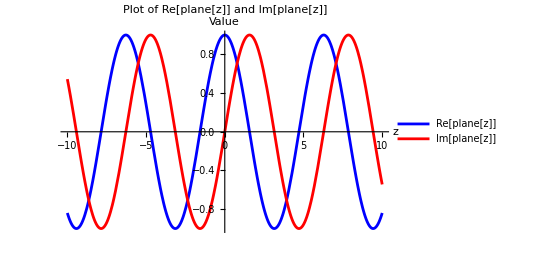

-Graphics-

```mathematica
(* Define the spherical harmonics function *)
sphericalHarmonic[l_, m_, theta_, phi_] := SphericalHarmonicY[l, m, theta, phi]

(* Set the azimuthal quantum number m to 0 *)
m = 0;

(* Define a list of l values to plot *)
lValues = {0, 1, 2, 3};

(* Plot the real part of the spherical harmonics for each l *)
plots = Table[
   SphericalPlot3D[
    Abs[Re[sphericalHarmonic[l, m, theta, phi]]], {theta, 0, Pi}, {phi, 0, 2 Pi},
    PlotLabel -> "l = " <> ToString[l],
    PlotRange -> All,
    ColorFunction -> "Rainbow",
    AxesLabel -> {"x", "y", "z"},
    Boxed -> False,
    Axes -> False
   ],
   {l, lValues}
];

(* Display the plots *)
GraphicsGrid[Partition[plots, 2]]
```

-Graphics-

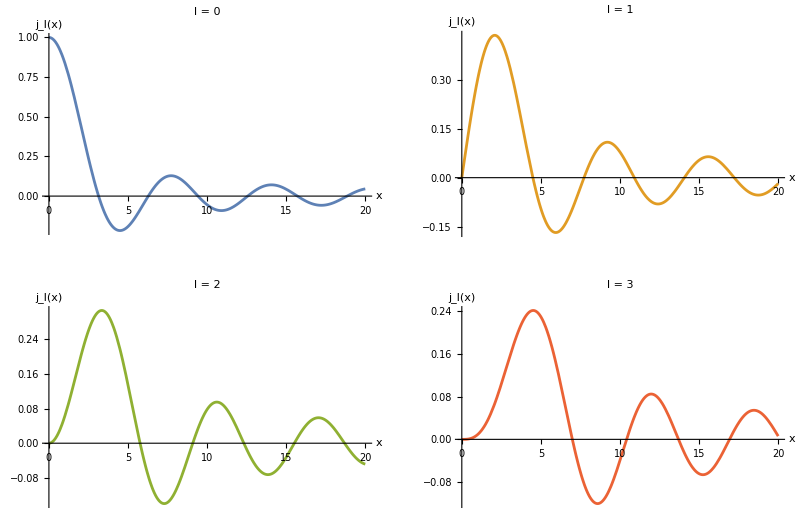

```mathematica
(* Define the range of x values *)
xRange = {x, 0,20};

(* Define a list of l values to plot *)
lValues = Range[0, 4];

(* Plot the spherical Bessel functions for each l *)
plots = Table[
   Plot[
    SphericalBesselJ[l, x], xRange,
    PlotLabel -> "l = " <> ToString[l],
    PlotRange -> All,
    AxesLabel -> {"x", "j_l(x)"},
    PlotStyle -> ColorData[97][l + 1]
   ],
   {l, lValues}
];

(* Display the plots *)
GraphicsGrid[Partition[plots, 2]]
```

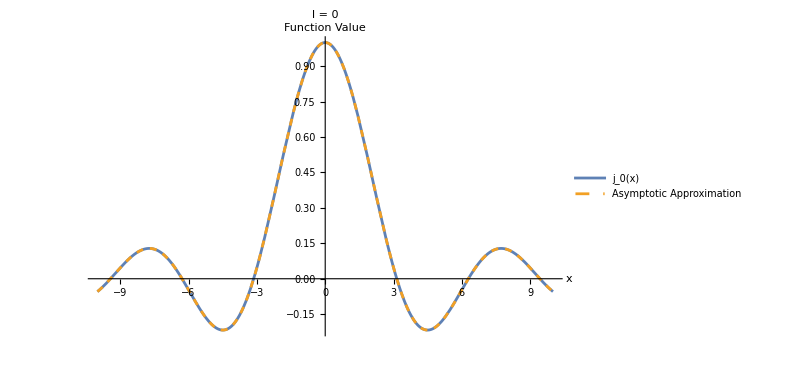

```mathematica
(* Define the range of x values *)
xRange = {x, -10, 10};

(* Define the value of l *)
l = 0;

(* Define the asymptotic function *)
asymptoticFunction[l_, k_, x_] := Sin[k x - l Pi/2];

(* Set a value for k *)
k = 1;

(* Plot the spherical Bessel function and its asymptotic approximation for l = 0 *)
Plot[
 {
  SphericalBesselJ[l, x],
  asymptoticFunction[l, k, x]/(k x)
 },
 xRange,
 PlotLabel -> "l = " <> ToString[l],
 PlotRange -> All,
 AxesLabel -> {"x", "Function Value"},
 PlotStyle -> {ColorData[97][l + 1], Dashed},
 PlotLegends -> {"j_0(x)", "Asymptotic Approximation"}
]
```

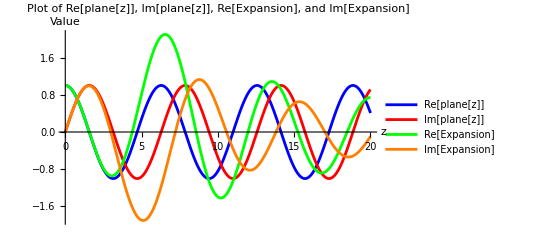

```mathematica
(* Define the value of k *)
k = 1;

(* Define the plane function *)
plane[z_] := Exp[I k z];

(* Define the spherical Bessel function *)
sphericalBesselJ[l_, x_] := SphericalBesselJ[l, x];

(* Define the Legendre polynomial *)
legendreP[l_, x_] := LegendreP[l, x];

(* Compute the spherical harmonics expansion for Exp[I k z] up to l = 4 *)
expansion[z_] := Sum[(2 l + 1) I^l sphericalBesselJ[l, k z] legendreP[l, 1], {l, 0, 4}];

(* Plot the real and imaginary parts of plane[z] and the expansion *)
Plot[
 {
  Re[plane[z]], 
  Im[plane[z]], 
  Re[expansion[z]], 
  Im[expansion[z]]
 },
 {z, 0, 20 k},
 PlotLegends -> {"Re[plane[z]]", "Im[plane[z]]", "Re[Expansion]", "Im[Expansion]"},
 PlotStyle -> {Blue, Red, Green, Orange},
 AxesLabel -> {"z", "Value"},
 PlotLabel -> "Plot of Re[plane[z]], Im[plane[z]], Re[Expansion], and Im[Expansion]"
]
```

-Graphics-

```mathematica
(*  I , E > V0*)
m = 930 ;
k1 = Sqrt[ 2 m (en + V0) ];
u1[r_] := a Exp[ I k1 r ] + b Exp[ - I k1 r];
(* II, E - V, imag*)
κ = Sqrt[ 2 m (V1 - en)];
u2[r_] := c Exp[ - κ r ] + d Exp[ κ r];
(* III, E > V0*)
k3 = Sqrt[ 2 m en];
u3[r_] := g Exp[ I k3 r ] + h Exp[ - I k3 r];
```

Transmission through Barrier
-Graphics-

```mathematica
(* Define the derivatives of the wave functions *)
u1Prime[r_] := D[u1[r], r];
u2Prime[r_] := D[u2[r], r];
u3Prime[r_] := D[u3[r], r];
(* Boundary conditions at r = r0 *)
eq1 = u1[Subscript[r, 0]] == u2[Subscript[r, 0]]
eq2 = u1Prime[Subscript[r, 0]] == u2Prime[Subscript[r, 0]]
(* Boundary conditions at r = r1 *)
eq3 = u2[Subscript[r, 1]] == u3[Subscript[r, 1]]
eq4 = u2Prime[Subscript[r, 1]] == u3Prime[Subscript[r, 1]]
(* Set a = 0 *)
eq1Zero = eq1 /. a -> 0
eq2Zero = eq2 /. a -> 0
```

b ⅇ^(-2 ⅈ √465 √(en+V0) r_0)+a ⅇ^(2 ⅈ √465 √(en+V0) r_0)==c ⅇ^(-2 √465 √(-en+V1) r_0)+d ⅇ^(2 √465 √(-en+V1) r_0)

-2 ⅈ √465 b ⅇ^(-2 ⅈ √465 √(en+V0) r_0) √(en+V0)+2 ⅈ √465 a ⅇ^(2 ⅈ √465 √(en+V0) r_0) √(en+V0)==-2 √465 c ⅇ^(-2 √465 √(-en+V1) r_0) √(-en+V1)+2 √465 d ⅇ^(2 √465 √(-en+V1) r_0) √(-en+V1)

c ⅇ^(-2 √465 √(-en+V1) r_1)+d ⅇ^(2 √465 √(-en+V1) r_1)==ⅇ^(2 ⅈ √465 √en r_1) g+ⅇ^(-2 ⅈ √465 √en r_1) h

-2 √465 c ⅇ^(-2 √465 √(-en+V1) r_1) √(-en+V1)+2 √465 d ⅇ^(2 √465 √(-en+V1) r_1) √(-en+V1)==2 ⅈ √465 ⅇ^(2 ⅈ √465 √en r_1) √en g-2 ⅈ √465 ⅇ^(-2 ⅈ √465 √en r_1) √en h

b ⅇ^(-2 ⅈ √465 √(en+V0) r_0)==c ⅇ^(-2 √465 √(-en+V1) r_0)+d ⅇ^(2 √465 √(-en+V1) r_0)

-2 ⅈ √465 b ⅇ^(-2 ⅈ √465 √(en+V0) r_0) √(en+V0)==-2 √465 c ⅇ^(-2 √465 √(-en+V1) r_0) √(-en+V1)+2 √465 d ⅇ^(2 √465 √(-en+V1) r_0) √(-en+V1)

```mathematica
(*Solve the system of equations for the parameter b*)solution=Solve[{eq1Zero,eq2Zero,eq3,eq4},{b,g}]
```

{}